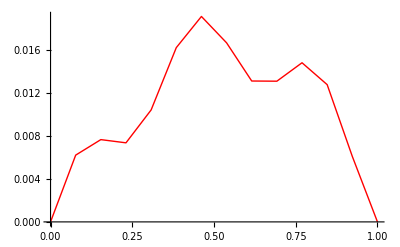

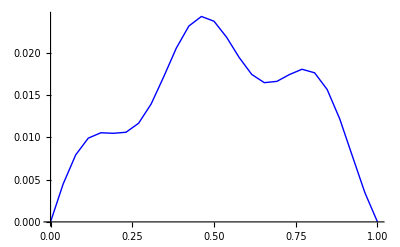

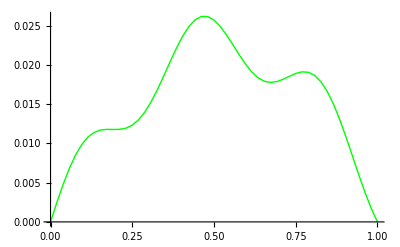

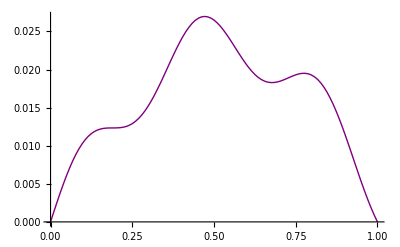

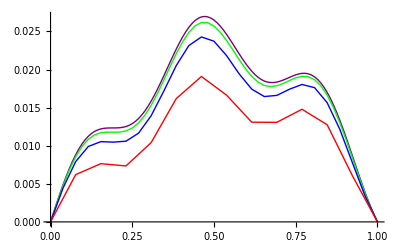

```mathematica
(* Need to reach form A*c = B, where A = Mat *)
ϕ[x_, xi_, h_]:=If[xi==1, 
Piecewise[{{0, 0≤x<xi-h}, {(x-(xi-h))/h, xi-h<x≤xi}}],
If[xi==0, Piecewise[{{(xi+h-x)/h, xi<x≤xi+h}}],
Piecewise [{{0, 0≤x<xi-h}, {(x-(xi-h))/h, xi-h<x≤xi}, {(xi+h-x)/h, xi<x≤xi+h}, {0, xi+h<x≤1}}]
]
];
MyFunc = Function[{n,mux,bex,six,fux},
INF = 1000000000;
myN =n+1;
h = 1/n;
(*preparing x[i]*)
xi = {};
start=0;
Do[
xi =AppendTo[xi,start];
start = start + h;
,{i,myN+1}];

(*preparing matrix*)
Mat = {{}};
tmp = {};
Do[tmp = AppendTo[tmp, 0], {i,myN}];
Do[Mat = AppendTo[Mat, tmp], {i,myN}];
Mat = Delete[Mat, {1}];


(*fill main diagonal*)
Mat[[myN]][[myN]] =Mat[[1]][[1]]=INF;
Do[
val = 0;
val = val + Integrate[mux*D[ϕ[x, xi[[i]], h], x]^2, {x, xi[[i-1]], xi[[i+1]]} ];
val = val + Integrate[bex*ϕ[x, xi[[i]]*D[ϕ[x, xi[[i]], h], x], h], {x, xi[[i-1]], xi[[i+1]]} ];
val = val + Integrate[six*ϕ[x, xi[[i]], h]^2, {x, xi[[i-1]], xi[[i+1]]} ];

Mat[[i]][[i]] = val;
, {i,2,myN-1,1}];


(*fill upper diagonal*)
Do[
val = 0;
val = val + Integrate[mux*D[ϕ[x, xi[[i]], h], x]*D[ϕ[x, xi[[i+1]], h], x], {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[bex*D[ϕ[x, xi[[i]], h], x]*ϕ[x, xi[[i+1]], h], {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[six*ϕ[x, xi[[i]], h]*ϕ[x, xi[[i+1]], h], {x, xi[[i]], xi[[i+1]]} ];
Mat[[i]][[i+1]] = val;
, {i,1,myN-1,1}];


(*fill bottom diagonal*)
Do[
val = 0;
val = val + Integrate[mux*D[ϕ[x, xi[[i+1]], h], x]*D[ϕ[x, xi[[i]], h], x], {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[bex*D[ϕ[x, xi[[i+1]], h], x]*ϕ[x, xi[[i]], h], {x, xi[[i]], xi[[i+1]]} ];
val = val + Integrate[six*ϕ[x, xi[[i]], h]*ϕ[x, xi[[i+1]], h], {x, xi[[i]], xi[[i+1]]} ];
Mat[[i+1]][[i]] = val;
, {i,1,myN-1,1}];


(*prepare B*)
B = {};
B = AppendTo[B, Integrate[fux *ϕ[x, xi[[2]], h], {x,xi[[1]],xi[[2]]}] ];
Do[
val = 0;
val = val + Integrate[fux*ϕ[x, xi[[i]], h], {x,xi[[i-1]],xi[[i]]}];
val = val + Integrate[fux*ϕ[x, xi[[i+1]], h], {x,xi[[i]],xi[[i+1]]}];
B = AppendTo[B, val];
, {i,2,myN-1,1}];
B = AppendTo[B, Integrate[fux*ϕ[x, xi[[myN]], h], {x,xi[[myN-1]],xi[[myN]]}] ];


res = Array[0,{myN}];
A = Mat;

(*
(*solve equation progonka*)
temp = 0;
A[[1]][[2]]  = A[[1]][[2]] /A[[1]][[1]];
B[[1]] =- B[[1]]/A[[1]][[1]];
For   [i=2, i<myN, i++,
 temp = 1/ (A[[i]][[i]]- A[[i-1]][[i]]*A[[i]][[i-1]] );
A[[i]][[i+1]] = A[[i]][[i+1]]*temp;
B[[i]] =(B[[i]]- B[[i-1]]*A[[i]][[i-1]] )*temp; 
]

res[[myN]] = -(A[[myN]][[myN-1]]*B[[myN-1]]- B[[myN]])/(A[[myN]][[myN]]- A[[myN]][[myN-1]]*A[[myN-1]][[myN]]);
For[i= myN-1, i>0, i--,
res[[i]] = B[[i]]- A[[i]][[i+1]]*res[[i+1]];
]
*)



   
res = LinearSolve[A,B];

Dots = {{}};
Do[
Dots = AppendTo[Dots,{xi[[i]], res[[i]]}];
,{i,myN}];

Dots = Delete[Dots,{1}];
Return[Dots];
];

(* Processing Data *)
n = 13;
mu= 1;
be=0;
si=-9;
fu=Sin[17*x];
X = MyFunc[n,mu,be,si,fu][[1]];
N[X];
g1 =ListLinePlot[X,PlotStyle -> Red, PlotRange->Full]
X2 = MyFunc[(2*n),mu,be,si,fu][[1]];
N[X2];
g2 =ListLinePlot[X2,PlotStyle -> Blue, PlotRange->Full]
X4 = MyFunc[(4*n),mu,be,si,fu][[1]];
N[X4];
g3 = ListLinePlot[X4,PlotStyle ->Green, PlotRange->Full]
X8 = MyFunc[(8*n),mu,be,si,fu][[1]];
N[X8];
g4 =ListLinePlot[X8,PlotStyle -> Purple, PlotRange->Full]
Show[g4,g3,g2, g1]
```

```mathematica
(*-------*)
(*-------*)
(*-NORMA-*)
(*-------*)
(*-------*)
ϕ[x_, xi_, h_]:=If[xi==1, 
Piecewise[{{0, 0≤x<xi-h}, {(x-(xi-h))/h, xi-h<x≤xi}}],
If[xi==0, Piecewise[{{(xi+h-x)/h, xi<x≤xi+h}}],
Piecewise [{{0, 0≤x<xi-h}, {(x-(xi-h))/h, xi-h<x≤xi}, {(xi+h-x)/h, xi<x≤xi+h}, {0, xi+h<x≤1}}]
]
];
BuildU[U_, n_, x_]:=∑_(i=1)^(n+1) U[[i, 2]]*ϕ[x, U[[i, 1]], U[[2, 1]]];
NormaL2 = Function [{Uh, Uh2, n1}, 

xnormaL2 = NIntegrate[(BuildU[Uh, n1/2, x]-BuildU[Uh2, n1, x])^2, {x, 0, 1}, MaxRecursion->15];

√xnormaL2

];



SingleNormaL2 = Function[{Uh, n1}, 

normaL2=NIntegrate[(BuildU[Uh, n1, x])^2, {x, 0, 1}, MaxRecursion->15];
√normaL2
];

SingleNormaH0 = Function[{Uh, n1}, 

normaH0=NIntegrate[(BuildU[Uh, n1, x])^2+(D[BuildU[Uh, n1, x], x])^2, {x, 0, 1}, MaxRecursion->15];

√normaH0

];

NormaH0 = Function [{Uh, Uh2, n1}, 
normaH0 = NIntegrate[(BuildU[Uh, n1/2, x]-BuildU[Uh2, n1, x])^2+(D[BuildU[Uh, n1/2, x]-BuildU[Uh2, n1, x], x])^2, {x, 0, 1}, MaxRecursion->15];

√normaH0
];

p=Log[2, NormaL2[X, X2, n*2]/NormaL2[X2, X4, n*4]];

Print ["Показник збіжності  L2    ",p];

(* Показуєм похибку *)

Pohybka = Array[0, {4, 4}];
Pohybka[[1]][[1]]=n;
Pohybka[[2]][[1]]=n*2;
Pohybka[[3]][[1]]=n*4;
Pohybka[[4]][[1]]=n*8;

Pohybka[[1]][[2]]=SingleNormaL2[X, n];
Pohybka[[2]][[2]]=SingleNormaL2[X2, n*2];
Pohybka[[3]][[2]]=SingleNormaL2[X4, n*4];
Pohybka[[4]][[2]]=SingleNormaL2[X8, n*8];

Pohybka[[1]][[3]]=0;
Pohybka[[2]][[3]]=NormaL2[X, X2, n*2];
Pohybka[[3]][[3]]=NormaL2[X2, X4, n*4];
Pohybka[[4]][[3]]=NormaL2[X4, X8, n*8];

Pohybka[[1]][[4]]=0;
Pohybka[[2]][[4]]=N[NormaL2[X, X2, n*2]/SingleNormaL2[X2, n*2]];
Pohybka[[3]][[4]]=N[NormaL2[X2, X4, n*4]/SingleNormaL2[X4, n*4]];
Pohybka[[4]][[4]]=N[NormaL2[X4, X8, n*8]/SingleNormaL2[X8, n*8]];



Print[TableForm[Pohybka,TableHeadings->{None,{"Кількість ітерацій","Норма", "Похибка","Відносна похибка"}}]];

p=Log[2, NormaH0[X, X2, n*2]/NormaH0[X2, X4, n*4]];

Print ["Показник збіжності  H1   ",p];

(* Показуєм похибку *)

Pohybka = Array[0, {4, 4}];
Pohybka[[1]][[1]]=n;
Pohybka[[2]][[1]]=n*2;
Pohybka[[3]][[1]]=n*4;
Pohybka[[4]][[1]]=n*8;

Pohybka[[1]][[2]]=SingleNormaH0[X, n];
Pohybka[[2]][[2]]=SingleNormaH0[X2, n*2];
Pohybka[[3]][[2]]=SingleNormaH0[X4, n*4];
Pohybka[[4]][[2]]=SingleNormaH0[X8, n*8];

Pohybka[[1]][[3]]=0;
Pohybka[[2]][[3]]=NormaH0[X, X2, n*2];
Pohybka[[3]][[3]]=NormaH0[X2, X4, n*4];
Pohybka[[4]][[3]]=NormaH0[X4, X8, n*8];

Pohybka[[1]][[4]]=0;
Pohybka[[2]][[4]]=NormaH0[X, X2, n*2]/SingleNormaH0[X2, n*2];
Pohybka[[3]][[4]]=NormaH0[X2, X4, n*4]/SingleNormaH0[X4, n*4];
Pohybka[[4]][[4]]=NormaH0[X4, X8, n*8]/SingleNormaH0[X8, n*8];



Print[TableForm[Pohybka,TableHeadings->{None,{"Кількість ітерацій","Норма", "Похибка","Відносна похибка"}}]];
```

Показник збіжності  L2    1.42423

Кількість ітерацій | Норма | Похибка | Відносна похибка
13 | 0.0120538 | 0 | 0
26 | 0.0155996 | 0.00357125 | 0.228932
52 | 0.0169144 | 0.00133071 | 0.0786732
104 | 0.017429 | 0.000524655 | 0.0301024

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in x near {x} = {0.0769346}. NIntegrate obtained 0.000345997 and 3.37575×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in x near {x} = {0.0769346}. NIntegrate obtained 0.0000744484 and 2.25912×10^-8 for the integral and error estimates.

Показник збіжності  H1   1.10822

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in x near {x} = {0.0769346}. NIntegrate obtained 0.00424948 and 2.06457×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 15 recursive bisections in x near {x} = {0.0769346}. NIntegrate obtained 0.00484362 and 2.14744×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.